```mathematica
(* Integers of a certain length which are divisible by #digits, prefixes also having that property *)
divCheck[x_]:=Divisible[x,Length[IntegerDigits[x]]]
extend[x_]:=Select[10x+Range[0,9],divCheck]
extendList[l_]:=Flatten[extend/@l]
```

```mathematica
numList=Length/@NestList[extendList,Range[9],25] (* counting the integers of each length *)
numCurve[x_]:=9*(10^(x-1))/(x!) (* heuristic prediction *)
```

{9,45,150,375,750,1200,1713,2227,2492,2492,2225,2041,1575,1132,770,571,335,180,90,44,18,12,6,3,1,0}

```mathematica
Nest[extendList,Range[9],24] (* Googleable result :) *)
```

{3608528850368400786036725}

```mathematica
lp=ListPlot[numList];
p=Plot[numCurve[x],{x,0,25}];
lop=ListLogPlot[numList];
op=LogPlot[numCurve[x],{x,0,25}];
```

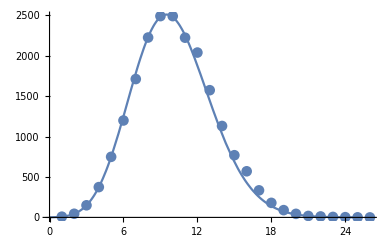

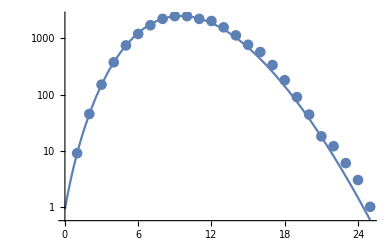

```mathematica
Show[lp,p] (* pretty plot *) 
Show[lop,op] (* pretty log plot *)
```

```mathematica
Plot[numCurve[x],{x,24.41122,24.41123}]; (* numCurve[x] = 1 *)
```

```mathematica
Plot[numCurve[x],{x,25.15,25.17}] ;(* numCurve[x] = 0.5 *)
```

```mathematica
(* OEIS A098143 *)
fullCheck[n_]:=If[n==0,True,And[divCheck[n],fullCheck[Floor[n/10]]]]
last[n_]:=If[extend[n]=={},n,last[First[extend[n]]]]
If[fullCheck[#],last[#],#]&/@Range[100]//TableForm;
```

```mathematica
(* generalization to any base *)
(*b=10;l=30;*)
divCheck[x_,b_]:=Divisible[x,Length[IntegerDigits[x,b]]]
extend[x_,b_]:=Select[b x+Range[0,b-1],divCheck[#,b]&]
extendList[l_,b_]:=Flatten[extend[#,b]&/@l]

numList[b_,n_]:=numList[b,n]=Length/@NestList[extendList[#,b]&,Range[b-1],n] (* counting the integers of each length *)
numCurve[b_,m_]:=(b-1)*(b^(m-1))/(m!) (* heuristic prediction *)

Clear[max]
max[base_]:=max[base]=
Module[{i=1,l=Range[base-1]},
While[Length[l]>0,i++;l=extendList[l,base]];
i-1]

(*N[numCurve[10,#]&/@Range[25+1]]
numList[10,30]
Position[numList[10,25],0][[1,1]]-1*)
```

```mathematica
max[15]//Timing
```

{348.532,38}

```mathematica
Timing[max/@Range[14]]
```

{127.536,{0,2,6,7,10,11,18,17,22,25,26,28,35,39}}

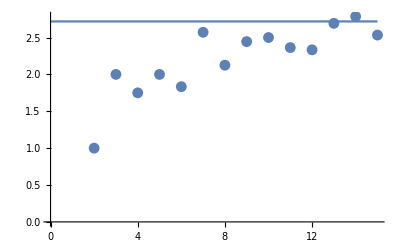

```mathematica
lp=ListPlot[Table[{bb,max[bb]/bb},{bb,2,15}]];
cp=Plot[E ,{x,0,15}];
Show[lp,cp]
```